### Start choosing the example:

```mathematica
t=24;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

EliminatorX: Good job!

DataToEquations: Done.

{0.024178,Null}

```mathematica
v0=MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j194→1,j195→3,j196→2,j197→3,j198→1,j199→2,j200→0,j201→0,j202→0,j203→0,j204→0,j205→0,jt206→0,jt207→1,jt208→1,jt209→1-1,jt210→1-1,jt211→-1+1,jt212→-1+1,jt213→3-1,jt214→0,jt215→2,jt216→3,jt217→0,u218→5,u219→4,u220→6,u221→1,u222→5,u223→6,u224→-1+5,u225→-3+4,u226→-2+6,u227→1,u228→5,u229→6|>

#### Non-linear case

```mathematica
alpha = 0;
beta = 0;
A = 0.2;
Parameters["alpha"] = alpha;
Parameters
```

<|alpha→0,beta→0,g[m]→Log,W[x,A]→Function[{x,a},a Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$8004[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$8004[x$]-g$8004[m$]]|>

```mathematica
MFGEquations["Nrhs"]
```

{j194-j200+Intg[j194-j200],j195-j201+Intg[j195-j201],j196-j202+Intg[j196-j202]}

```mathematica
FixedSolverStepX1[MFGEquations]@ MFGEquations["criticalreduced1"][[2]]//KeySort
```

Possible multiple solutions 
{False,<|j198→1,j199→2,u227→1,j194→1,j195→3,j196→2,j197→3,j200→0,j201→0,j202→0,j203→0,j204→0,j205→0,jt206→0,jt207→1,jt209→1-1,jt210→1-1,jt211→-1+1,jt212→-1+1,jt213→3-1,jt214→0,jt215→2,jt216→3,jt217→0,u221→1,u224→-1+5,u225→-3+4,u226→-2+6,u228→5,u229→6,u219→4,u222→5,u223→6,jt208→1,u218→5,u220→6|>}

<|j198→1,j199→2,u227→1,j194→1,j195→3,j196→2,j197→3,j200→0,j201→0,j202→0,j203→0,j204→0,j205→0,jt206→0,jt207→1,jt209→1-1,jt210→1-1,jt211→-1+1,jt212→-1+1,jt213→3-1,jt214→0,jt215→2,jt216→3,jt217→0,u221→1,u224→-1+5,u225→-3+4,u226→-2+6,u228→5,u229→6,u219→4,u222→5,u223→6,jt208→1,u218→5,u220→6|>

{}

<|j194→1,j195→3,j196→2,j197→3,j198→1,j199→2,j200→0,j201→0,j202→0,j203→0,j204→0,j205→0,jt206→0,jt207→1,jt208→1,jt209→1-1,jt210→1-1,jt211→-1+1,jt212→-1+1,jt213→3-1,jt214→0,jt215→2,jt216→3,jt217→0,u218→5,u219→4,u220→6,u221→1,u222→5,u223→6,u224→-1+5,u225→-3+4,u226→-2+6,u227→1,u228→5,u229→6|>

```mathematica
FixedSolverStepX1[MFGEquations]@%//KeySort
```

Possible multiple solutions 
{False,<|j194→1,j195→3,j196→2,j197→3,j198→1,j199→2,j200→0,j201→0,j202→0,j203→0,j204→0,j205→0,jt206→0,jt207→1,jt208→1,jt209→1-1,jt210→1-1,jt211→-1+1,jt212→-1+1,jt213→3-1,jt214→0,jt215→2,jt216→3,jt217→0,u218→5,u219→4,u220→6,u221→1,u222→5,u223→6,u224→-1+5,u225→-3+4,u226→-2+6,u227→1,u228→5,u229→6|>}

<|j194→1,j195→3,j196→2,j197→3,j198→1,j199→2,j200→0,j201→0,j202→0,j203→0,j204→0,j205→0,jt206→0,jt207→1,jt208→1,jt209→1-1,jt210→1-1,jt211→-1+1,jt212→-1+1,jt213→3-1,jt214→0,jt215→2,jt216→3,jt217→0,u218→5,u219→4,u220→6,u221→1,u222→5,u223→6,u224→-1+5,u225→-3+4,u226→-2+6,u227→1,u228→5,u229→6|>

{}

<|j194→1,j195→3,j196→2,j197→3,j198→1,j199→2,j200→0,j201→0,j202→0,j203→0,j204→0,j205→0,jt206→0,jt207→1,jt208→1,jt209→1-1,jt210→1-1,jt211→-1+1,jt212→-1+1,jt213→3-1,jt214→0,jt215→2,jt216→3,jt217→0,u218→5,u219→4,u220→6,u221→1,u222→5,u223→6,u224→-1+5,u225→-3+4,u226→-2+6,u227→1,u228→5,u229→6|>

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]]//N,11, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

Possible multiple solutions 
{False,<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>}

<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>

{}

Possible multiple solutions 
{False,<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>}

<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>

{}

Possible multiple solutions 
{False,<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>}

<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>

{}

Possible multiple solutions 
{False,<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>}

<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>

{}

Possible multiple solutions 
{False,<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>}

<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>

{}

Possible multiple solutions 
{False,<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>}

<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>

{}

Possible multiple solutions 
{False,<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>}

<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>

{}

Possible multiple solutions 
{False,<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>}

<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>

{}

Possible multiple solutions 
{False,<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>}

<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>

{}

Possible multiple solutions 
{False,<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>}

<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>

{}

Possible multiple solutions 
{False,<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>}

<|j198→1.,j199→2.,u227→1.,j194→1.,j195→3.,j196→2.,j197→3.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1.,u224→4.,u225→1.,u226→4.,u228→5.,u229→6.,u219→4.,u222→5.,u223→6.,jt208→1.,u218→5.,u220→6.|>

{}

<|j194→1.,j195→3.,j196→2.,j197→3.,j198→1.,j199→2.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt208→1.,jt209→0.,jt210→0.,jt211→0.,jt212→0.,jt213→2.,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u218→5.,u219→4.,u220→6.,u221→1.,u222→5.,u223→6.,u224→4.,u225→1.,u226→4.,u227→1.,u228→5.,u229→6.|>

```mathematica
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol1
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol2
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol3n
```

2.01703

0.

0.

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced1"][[2]],10, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

EqEliminartorX2: Count!

The system is False. Returning the inputs.

EqEliminartorX2: Count!

The system is False. Returning the inputs.

FixedX2: next step: j194-j200-u218+u224==0.294244&&j195-j201-u219+u225==1.75292&&j196-j202-u220+u226==0.953469

EqEliminartorX2: Count!

The system is False. Returning the inputs.

EqEliminartorX2: Count!

The system is False. Returning the inputs.

FixedX2: next step: j194-j200-u218+u224==0.294244&&j195-j201-u219+u225==1.75292&&j196-j202-u220+u226==0.953469

<|j194→1.,j195→3.,j196→2.,j197→3.,j198→1.,j199→2.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→1.-1. jt208,jt210→1.-1. jt208,jt211→-1.+1. jt208,jt212→-1.+1. jt208,jt213→3.-1. jt208,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1,u224→-0.705756+1. u218,u225→-1.24708+1. u219,u226→-1.04653+1. u220,u227→1,u228→u222,u229→u223|>

```mathematica
nsol3n=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced1"][[2]],10, SameTest->(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

The system is False. Returning the inputs.

FixedX3: next step: j194-j200-u218+u224==0.294244&&j195-j201-u219+u225==1.75292&&j196-j202-u220+u226==0.953469

The system is False. Returning the inputs.

FixedX3: next step: j194-j200-u218+u224==0.294244&&j195-j201-u219+u225==1.75292&&j196-j202-u220+u226==0.953469

<|j194→1.,j195→3.,j196→2.,j197→3.,j198→1.,j199→2.,j200→0.,j201→0.,j202→0.,j203→0.,j204→0.,j205→0.,jt206→0.,jt207→1.,jt209→1.-1. jt208,jt210→1.-1. jt208,jt211→-1.+1. jt208,jt212→-1.+1. jt208,jt213→3.-1. jt208,jt214→0.,jt215→2.,jt216→3.,jt217→0.,u221→1,u224→-0.705756+1. u218,u225→-1.24708+1. u219,u226→-1.04653+1. u220,u227→1,u228→u222,u229→u223|>

### What is this plot for?

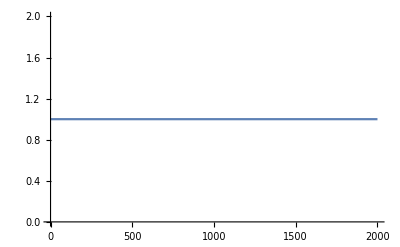
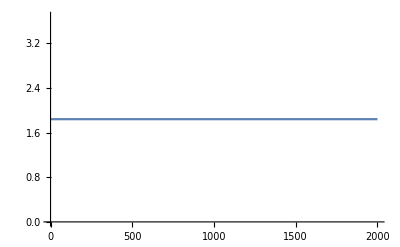
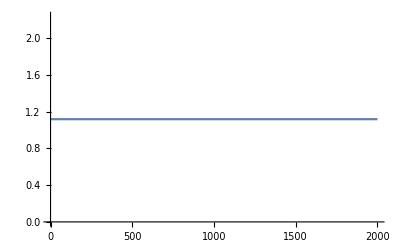
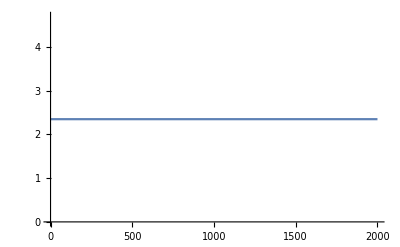
<|{2,1->2}→-Graphics-,{ex746,1->ex746}→-Graphics-,{3,2->3}→-Graphics-,{ex747,3->ex747}→-Graphics-,{2,en745->2}→-Graphics-,{1,1->2}→-Graphics-,{1,1->ex746}→-Graphics-,{2,2->3}→-Graphics-,{3,3->ex747}→-Graphics-,{en745,en745->2}→-Graphics-|>

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.

```mathematica
f=<|c->b|>
```

<|c→b|>

```mathematica
AssociateTo[f,v->m]
```

<|c→b,v→m|>

```mathematica
f
```

<|c→b,v→m|>

```mathematica
f
```

<|c→b,v→m|>

```mathematica
Append[f,m->b]
```

<|c→b,v→m,m→b|>

```mathematica
f
```

<|c→b,v→m|>

```mathematica
AssociateTo[f,m->b]
```

<|c→b,v→m,m→b|>

```mathematica
f
```

<|c→b,v→m,m→b|>

```mathematica
f=Append[f,g->k]
```

<|c→b,v→m,m→b,g→k|>

```mathematica
f
```

<|c→b,v→m,m→b,g→k|>

```mathematica
Reduce[j589==0.+1. j589&&j589==0.+1. j589]
```

True

```mathematica
Solve[x^3 ==1, Reals]
```

{{x→1}}

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

$Aborted